```mathematica
<<Wolfram`QuantumFramework`
```

### 14.1 [MSc] How do I compute and compare the Shannon and von Neumann entropies?

Regarding quantum state there is only one  basic formula . For a probability distribution p and for a state ρ we can define H(p)= - ∑_i p_i log_2 p_i,  S(ρ)= -Tr(ρ log_2 ρ)= H(spectrum ρ), with the convention 0 log 0 so pure states have entropy equal to 0. Reading S as H of the eigenvalue list is the whole content of the second equality, since a matrix function acts on eigenvalues and leaves eigenvectors alone.

So “comparing” the two is only a question once a distribution is named, and the honest comparison is against the one an experiment actually produces. Measuring ρ in some orthonormal basis {|i⟩} gives outcome probabilities p_i= ⟨i|ρ|i⟩ , the diagonal of ρ in that basis, so H(p)≥S(ρ) with equality when the basis is exactly the eigenbasis of ρ. For the mixed qubit state ρ=1/2(I+r⃗· σ⃗)  the two sides become one function of one variable each. The spectrum is (1±|r⃗|)/2 and the Z outcomes (1±r_z)/2, if we define h(x)=-x log_2 x-(1-x)log_2(1-x) then S(ρ)=h((1+|r⃗|)/2), H(p_z)=h((1+r_z)/2). And since h((1+r)/2) decreases as the radius r grows |r_z|≤ |r⃗|always, the inequality is exactly the statement that the measured radius cannot exceed the true one

WL:

Define the mixed qubit density matrix:

```mathematica
rho=1/2 (IdentityMatrix[2]+{rx,ry,rz}.PauliMatrix[{1,2,3}])
```

{{(1+rz)/2,1/2 (rx-ⅈ ry)},{1/2 (rx+ⅈ ry),(1-rz)/2}}

Define H(p):

```mathematica
shannon[p_]:=-#.Log[2,#]&@DeleteCases[p,0]
```

The spectrum depends on the Bloch vector only through its length:

```mathematica
Simplify[Eigenvalues[rho],Element[{rx,ry,rz},Reals]]
```

{1/2 (1-√(rx^2+ry^2+rz^2)),1/2 (1+√(rx^2+ry^2+rz^2))}

The von Neumann entropy computed from its definition as a matrix function, and the claim that it is the Shannon entropy of that spectrum:

```mathematica
Simplify[FullSimplify[-Tr[rho.MatrixLog[rho]]/Log[2],rx^2+ry^2+rz^2≤1]/.rx^2+ry^2+rz^2->r^2,r>0]
```

(r Log[(1-r)/(1+r)]+Log[-4/(-1+r^2)])/Log[4]

```mathematica
Simplify[-Tr[rho.MatrixLog[rho]]/Log[2]==shannon[Eigenvalues[rho]],rx^2+ry^2+rz^2≤1]
```

True

A measurement in the computational basis reads the diagonal, and its Shannon entropy is a different number built from the same formula:

```mathematica
{Diagonal[rho],shannon[Diagonal[rho]]}
```

{{(1+rz)/2,(1-rz)/2},-((1-rz) Log[(1-rz)/2])/(2 Log[2])-((1+rz) Log[(1+rz)/2])/(2 Log[2])}

The comparison needs no search. The binary entropy falls as the radius grows, and the measured radius |r_z|  never exceeds the true radius |r⃗|  so the measured distribution is the more spread of the two:

```mathematica
{Simplify[D[shannon[{(1+r)/2,(1-r)/2}], r]≤0,0≤r<1],Reduce[∀_({rx,ry,rz},{rx,ry,rz}∈Reals)Abs[rz]≤√(rx^2+ry^2+rz^2)]}
```

{True,True}

Equality holds exactly on the z axis, where the computational basis diagonalizes ρ:

```mathematica
N[(shannon[Diagonal[rho]]-shannon[Eigenvalues[rho]])/. {rx->1/3,ry->1/4,rz->1/5}]
```

0.131055

Off that axis the gap is a positive number of bits, the coherence the measurement threw away:

```mathematica
{shannon[Eigenvalues[rho]/. {rx->1,ry->0,rz->0}],shannon[Diagonal[rho]/. {rx->1,ry->0,rz->0}],shannon[Diagonal[rho]/. {rx->0,ry->0,rz->1}]}
```

{0,1,0}

QF:

Property  “VonNeumannEntropy” available for quantum states, result in bits:

```mathematica
VNentropy =QuantumState[rho]["VonNeumannEntropy"]
```

(Log[4]+(-1+√(rx^2+ry^2+rz^2)) Log[1-√(rx^2+ry^2+rz^2)]-(1+√(rx^2+ry^2+rz^2)) Log[1+√(rx^2+ry^2+rz^2)])/Log[4] b

Simplify to recover the previous result:

```mathematica
Simplify[FullSimplify[VNentropy,rx^2+ry^2+rz^2≤1]/.rx^2+ry^2+rz^2->r^2,r>0]
```

(r Log[(1-r)/(1+r)]+Log[-4/(-1+r^2)])/Log[4] b

The Shannon side belongs to the measurement rather than to the state, a QuantumMeasurement reports the entropy of its own outcome distribution, which is the diagonal the Z observable exposes (second argument directly extracts entropy in bits):

```mathematica
Simplify[QuantumMeasurementOperator["Z"][QuantumState[rho]]["Entropy",2]==shannon[Diagonal[rho]],rx^2+ry^2+rz^2≤1]
```

True

On the z axis the observable and the state share an eigenbasis, and the two entropies coincide as objects, not merely numerically:

```mathematica
With[{diagonal=rho/. {rx->0,ry->0}},Simplify[
QuantumState[diagonal]["VonNeumannEntropy",2]==QuantumMeasurementOperator["Z"][QuantumState[diagonal]]["Entropy",2],-1<rz<1]]
```

True

The pure equatorial state is the sharpest case , no mixedness at all, one full bit of measurement randomness:

```mathematica
{QuantumState["+"]["VonNeumannEntropy",2],QuantumMeasurementOperator["Z"][QuantumState["+"]]["Entropy",2]}
```

{0,1}

The maximum is set by dimension S <= log_2 d, reached only by the maximally mixed state:

```mathematica
With[{d=5},QuantumState["UniformMixture",d]["VonNeumannEntropy",2]==Log[2,d]]
```

True

### 14.2 [MSc] How do I compute the quantum relative entropy and check its non-negativity?

The relative entropy is defined as S(ρ || σ)=Tr(ρ(log_2 ρ-log_2 σ))=-S(ρ)-Tr(ρ log_2 σ) and Klein’s inequality says the answer is never negative,  S(ρ∥σ)≥0, with equality only at ρ=σ. Two properties keep it from being a distance. It is not symmetric, so S(ρ∥σ) and S(σ∥ρ) are different numbers and one must say which is meant, and is not even finite in general.  The infinity is physical rather than pathological. If σ assigns probability zero to an outcome that ρ allows, then a single measurement can rule σ out with certainty, so no finite amount of evidence is needed to separate them.

Two special cases anchor the general statement. Against the maximally mixed state the definition collapses to the entropy bound S(ρ || I/d)=log_2 d-S(ρ) so non negativity there is exactly the statement  S(ρ)≤log_2 d  And when ρ and σ commute, both are diagonal in one basis and the quantity reduces to ∑_i p_i log_2(p_i/q_i)  of their spectra, so the quantum statement contains the classical one rather than replacing it.

WL:

Bloch state builder:

```mathematica
bloch[v_]:=1/2 (IdentityMatrix[2]+v.PauliMatrix[{1,2,3}])
```

Relative entropy definition:

```mathematica
relativeEntropy[a_,b_]:=Tr[a.(MatrixLog[a]-MatrixLog[b])]/Log[2]
```

It vanishes when the two states agree, identically in the Bloch vector rather than at sampled points:

```mathematica
Simplify[relativeEntropy[bloch[{rx,ry,rz}],bloch[{rx,ry,rz}]],rx^2+ry^2+rz^2≤1]
```

0

Against the maximally mixed state it is the entropy bound in disguise, which is the one case where non-negativity is provable in closed form:

```mathematica
Simplify[relativeEntropy[bloch[{rx,ry,rz}],IdentityMatrix[2]/2]==1+Tr[bloch[{rx,ry,rz}].MatrixLog[bloch[{rx,ry,rz}]]]/Log[2],rx^2+ry^2+rz^2≤1]
```

True

Written in the Bloch radius, no radius makes it negative, so Reduce returns False for the whole search:

```mathematica
Reduce[1+(1/2 (1+r) Log[2,(1+r)/2]+1/2 (1-r) Log[2,(1-r)/2])<0&&0≤r<1,r,Reals]
```

False

For a general pair the symbolic form is unwieldy, so the check is a sampled one: two hundred independent pairs drawn uniformly from the Bloch ball, none of them negative:

```mathematica
Min@Table[Re[relativeEntropy@@(bloch/@RandomPoint[Ball[{0,0,0}],2])],200]
```

0.0252171

Equality is sharp, moving the second state by one part in a hundred already costs a positive number of bits:

```mathematica
Chop@N@{relativeEntropy[bloch[{1/5,0,1/2}],bloch[{1/5,0,1/2}]],relativeEntropy[bloch[{1/5,0,1/2}],bloch[{1/5,0,51/100}]]}
```

{0,0.0000996474}

Driving σ to a pure state closes its support and the quantity diverges, which is the limit rather than an error:

```mathematica
lim_(eps->0^+) relativeEntropy[IdentityMatrix[2]/2,bloch[{0,0,1-eps}]]
```

∞

For commuting states it is the classical divergence, whose minimum over the whole square is zero, attained only on the diagonal p=q:

```mathematica
Chop@NMinimize[{p Log[2,p/q]+(1-p) Log[2,(1-p)/(1-q)],0<p<1,0<q<1},{p,q}]
```

{0,{p→0.748843,q→0.748843}}

QF:

The framework carries it as a named distance, returning a Quantity in bits like the entropies of 14.1. On a pair of well separated mixed states it agrees with the definition:

```mathematica
vs=RandomPoint[Ball[{0,0,0}],2];
{QuantumDistance[Apply[Sequence,QuantumState["BlochVector"[#]]&/@vs],"RelativeEntropy"][[1]],Chop[relativeEntropy[Apply[Sequence,bloch/@vs]]]}
```

{1.3208,1.3208}

Define a pure and a mixed state:

```mathematica
ρ = QuantumState["RandomMixed"];
ψ = QuantumState["0"];
```

S(ρ||σ)!=S(σ||ρ) and can be infinite when σ is pure, unless ρ=σ that is zero:

```mathematica
QuantumDistance[ψ,ρ,"RelativeEntropy"]
```

1.32826 b

```mathematica
QuantumDistance[ρ,ψ,"RelativeEntropy"]
```

∞ b

```mathematica
QuantumDistance[ρ,ρ,"RelativeEntropy"]
```

0 b

It is non-negative:

```mathematica
Min[QuantumDistance[#1,#2,"RelativeEntropy"]&@@@Table[QuantumState["RandomMixed"],50,2]]
```

0.0551472 b

Compute symbolic “RelativeEntropy” using ρ as a generic mixed Bloch vector state and the states |0⟩ and |1⟩

```mathematica
FullSimplify[QuantumDistance[#,QuantumState["BlochVector"[{x,y,z}]],"RelativeEntropy"]&/@{QuantumState["0"],QuantumState["1"]},x^2+y^2+z^2<=1]
```

{(-(2 z ArcTanh[√(x^2+y^2+z^2)])/(√(x^2+y^2+z^2))+Log[-4/(-1+x^2+y^2+z^2)])/Log[4] b,-((x^2+y^2) (Log[1/2-1/2 √(x^2+y^2+z^2)]/(x^2+y^2+z^2-z √(x^2+y^2+z^2))+Log[1/2 (1+√(x^2+y^2+z^2))]/(x^2+y^2+z (z+√(x^2+y^2+z^2)))))/(2 Log[2]) b}

### 14.3 [MSc] How do I compute joint, conditional, and mutual quantum entropies (and find a negative conditional entropy)?

WL:

The von Neumann entropy read off the spectrum, so that the 0log0=0 convention acts on a state with rank-deficient support:

```mathematica
vonNeumann[m_]:=-#.Log[2,#]&@DeleteCases[Eigenvalues[m],0]
```

Each marginal is a contraction of the reshaped density matrix over the other factor’s pair of indices:

```mathematica
reduceA[m_]:=TensorContract[ArrayReshape[m,{2,2,2,2}],{{2,4}}]
reduceB[m_]:=TensorContract[ArrayReshape[m,{2,2,2,2}],{{1,3}}]
```

The Schmidt family as a density matrix:

```mathematica
MatrixForm[rhoAB=Simplify[With[{psi={Cos[t],0,0,Sin[t]}},Outer[Times,psi,Conjugate[psi]]],t∈Reals]]
```

(Cos[t]^2 | 0 | 0 | Cos[t] Sin[t]
0 | 0 | 0 | 0
0 | 0 | 0 | 0
Cos[t] Sin[t] | 0 | 0 | Sin[t]^2)

Three arguments, the two parts and the whole:

```mathematica
{sA,sB,sAB}=Simplify[vonNeumann/@{reduceA[rhoAB],reduceB[rhoAB],rhoAB},0<t<Pi/2]
```

{-(2 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2],-(2 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2],0}

The joint, conditional and mutual entropies are assembled from those three by the definitions above:

```mathematica
Simplify[{sAB,sAB-sB,sA+sB-sAB},0<t<Pi/2]
```

{0,(2 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2],-(4 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2]}

Measured in units of the marginal entropy, which is positive across the open interval, they collapse to constants: the whole family has one and the same entropic structure, only rescaled but we see is possible to get a negative value:

```mathematica
%/sA
```

{0,-1,2}

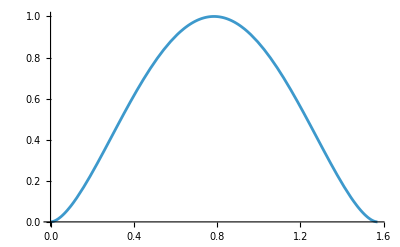

```mathematica
Plot[sA,{t,0,π/2}]
```

The extreme values over the family, the lowest conditional entropy and the highest mutual information are reached at the same angle:

```mathematica
FullSimplify@{Minimize[{sAB-sB,0<=t<=Pi/2},t],Maximize[{sA+sB-sAB,0<=t<=Pi/2},t]}
```

{{-1,{t→π/4}},{2,{t→π/4}}}

Erasing the one coherence between the two Schmidt terms leaves a state with the same populations, correlated but only classically:

```mathematica
dephased=DiagonalMatrix[Diagonal[rhoAB]]
```

{{Cos[t]^2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,Sin[t]^2}}

Dephasing in the Schmidt basis leaves both marginals untouched, so S(A) and S(B) are the same numbers as before:

```mathematica
Simplify[{reduceA[dephased],reduceB[dephased]}=={reduceA[rhoAB],reduceB[rhoAB]},0<t<Pi/2]
```

True

The two surviving inequalities are claims about every state, and the pure family is too narrow to test them, so draw mixed states at random from a Ginibre matrix normalized to unit trace:

```mathematica
randomState:=#/Tr[#]&@(#.ConjugateTranspose[#]&)@RandomComplex[{-1-I,1+I},{4,4}]
```

Subadditivity needs no sampling once the mutual information is recognized as the relative entropy against the product of marginals, an identity a single generic state already exposes:

```mathematica
Chop[Re[With[{r=randomState},Tr[r.(MatrixLog[r]-MatrixLog[KroneckerProduct[reduceA[r],reduceB[r]]])]/Log[2]-(vonNeumann[reduceA[r]]+vonNeumann[reduceB[r]]-vonNeumann[r])]]]
```

0

The Araki-Lieb bound is the one that limits how negative a conditional entropy can get, and its slack over two hundred random mixed states stays on one side of zero:

```mathematica
Positive@Chop@Re@Min@Table[With[{r=randomState},vonNeumann[r]-Abs[vonNeumann[reduceA[r]]-vonNeumann[reduceB[r]]]],200]
```

True

QF:

Define the family state:

```mathematica
qs=QuantumState[{Cos[t],0,0,Sin[t]}]
```

cos(t)00+sin(t)11

The marginals are partial traces:

```mathematica
{qa,qb}=QuantumPartialTrace[qs,#]&/@{{2},{1}};
```

The same three quantities, each entropy read off its own object with base 2 selected by the second argument:

```mathematica
qtriple=Simplify[{qs["VonNeumannEntropy",2],qs["VonNeumannEntropy",2]-qb["VonNeumannEntropy",2],qa["VonNeumannEntropy",2]+qb["VonNeumannEntropy",2]-qs["VonNeumannEntropy",2]},0<t<Pi/2]
```

{0,(2 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2],-(4 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2]}

```mathematica
qtriple===Simplify[{sAB,sAB-sB,sA+sB-sAB},0<t<Pi/2]
```

True

Two of the three are named quantities. “MutualInformationI” assembles  I(A:B) from the same three entropies, and “EntanglementEntropy” is the marginal entropy, which on a pure state is minus the conditional entropy; both carry a unit, as the entropies of 14.1 do:

```mathematica
Simplify[QuantumEntanglementMonotone[qs,#]&/@{"MutualInformationI","EntanglementEntropy"},0<t<Pi/2]
```

{-(4 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2] b,-(2 (Cos[t]^2 Log[Cos[t]]+Log[Sin[t]] Sin[t]^2))/Log[2] b}

```mathematica
QuantityMagnitude[%]===({sA+sB-sAB,sB-sAB})
```

True

Mutual information counts total correlation, classical included, so it is positive on a separable state,  take the maximally entangled state with its coherence erased:

```mathematica
qdephased=1/2 Sum[QuantumState[i]["MatrixState"],{i,{"00","11"}}]
```

1/2 0000+1/2 1111

Its mutual information is a full bit, while the default entanglement test, which uses the realignment criterion, reports the state separable:

```mathematica
{QuantumEntanglementMonotone[qdephased,"MutualInformationI"],QuantumEntangledQ[qdephased]}
```

{1 b,False}

Using QuantumEntangledQ with the “MutualInformationI” criteria returns Indeterminate for a maximally entangled state as readily as for this separable one, so the answer is not conclusive about the state:

```mathematica
QuantumEntangledQ[#,{{1},{2}},"MutualInformationI"]&/@{qdephased,QuantumState["PhiPlus"]}
```

{Indeterminate,Indeterminate}

### 14.4 [MSc] How do I compute the coherent information I_c(ρ, 𝒩)=S(𝒩(ρ))-S((𝒩⊗id)|ψ_p⟩⟨ψ_p|) of a state through a channel?

The entropy of the output alone cannot say how much quantum information survived a channel. A channel that discards its input and emits a fixed pure state has a zero-entropy output and has destroyed everything, so the quantity has to be told what went in. Purify ρ into |ψ_p⟩_RA, so that an untouched reference R holds a perfect record of A, send A alone through 𝒩, and weigh what the output keeps of that record against what the pair keeps

For a concrete channel take amplitude damping, an excited state decaying to the ground state with probability γ, with Kraus operators 
K_0=(1 | 0
0 | √(1-γ)), K_1=(0 | √γ
0 | 0) on the family of states ρ_p=(1-p)|0⟩ ⟨0|+p |1⟩ ⟨1|. That family is the one that decides this channel, damping commutes with rotations about z, so a coherence between the two levels contributes nothing the diagonal does not already carry, and the last cell below prices what an off-axis state costs

WL:

The entropy functional, read off the spectrum so the 0log0=0 convention acts:

```mathematica
vonNeumann[m_]:=-#.Log[2,#]&@DeleteCases[Eigenvalues[m],0]
```

Every state below turns out diagonal, so the binary entropy is the closed form to compare against:

```mathematica
h2[x_]:=-x Log[2,x]-(1-x) Log[2,1-x]
```

Define the amplitude damping channel by its Kraus operators:

```mathematica
kraus={{{1,0},{0,√(1-γ)}},{{0,√γ},{0,0}}}
```

{{{1,0},{0,√(1-γ)}},{{0,√γ},{0,0}}}

A Kraus set is a channel only if it preserves the trace, which is a condition on the operators alone:

```mathematica
Simplify[Total[ConjugateTranspose[#].#&/@kraus]==IdentityMatrix[2],0<γ<1]
```

True

The purification of  ρ_p in Schmidt form:

```mathematica
psi={Sqrt[1-p],0,0,Sqrt[p]}
```

{√(1-p),0,0,√p}

It is a purification because tracing the reference away returns the state it was built from:

```mathematica
Simplify[TensorContract[ArrayReshape[Outer[Times,psi,Conjugate[psi]],{2,2,2,2}],{{2,4}}]==DiagonalMatrix[{1-p,p}],0<p<1]
```

True

The channel acts on the first factor only, the reference passing through untouched:

```mathematica
rhoRB=Simplify[Total[With[{k=KroneckerProduct[#,IdentityMatrix[2]]},k.Outer[Times,psi,Conjugate[psi]].ConjugateTranspose[k]]&/@kraus],0<p<1&&0<γ<1]
```

(1-p | 0 | 0 | √((γ-1) (p-1) p)
0 | γ p | 0 | 0
0 | 0 | 0 | 0
√((γ-1) (p-1) p) | 0 | 0 | p-γ p)

The output on its own is that state with the reference traced away:

```mathematica
rhoB=TensorContract[ArrayReshape[rhoRB,{2,2,2,2}],{{2,4}}]
```

(γ p-p+1 | 0
0 | p-γ p)

The two entropies the definition asks for:

```mathematica
{entB,entRB}=FullSimplify[vonNeumann/@{rhoB,rhoRB},0<p<1&&0<γ<1]
```

{((-1+p-p γ) Log[1+p (-1+γ)]+p (-1+γ) Log[p-p γ])/Log[2],(2 p γ ArcTanh[1-2 p γ]-Log[1-p γ])/Log[2]}

Both are binary entropies of a damped population, one of what survives and one of what leaks:

```mathematica
FullSimplify[{entB,entRB}=={h2[(1-γ) p],h2[γ p]},0<p<1&&0<γ<1]
```

True

The complementary channel sends the input to the environment, its matrix elements the overlaps of the Kraus operators in that state:

```mathematica
rhoE=Outer[Tr[#1.DiagonalMatrix[{1-p,p}].ConjugateTranspose[#2]]&,kraus,kraus,1]
```

(√(1-γ) p Conjugate[√(1-γ)]-p+1 | 0
0 | √γ p Conjugate[√γ])

The environment’s entropy is the pair’s, which is the Stine-spring identity and the second form of I_c:

```mathematica
FullSimplify[vonNeumann[rhoE]==entRB,0<p<1&&0<γ<1]
```

True

Which of the two binary entropies wins is settled by monotonicity, since the binary entropy rises across the lower half of its range:

```mathematica
Simplify[D[h2[x],x]>0,0<x<1/2]
```

True

The best any input can do, below the threshold γ=1/2, at it and above it. Only the first of the three maximizers means anything the other two report a tie when the state is pure:

```mathematica
FullSimplify@Table[Maximize[{h2[(1-γ) x]-h2[γ x],0<=x<=1},x],{γ,{1/4,1/2,3/4}}]
```

{{Log[4/3]/Log[2],{x→4/9}},{0,{x→0}},{0,{x→1}}}

At γ=1/2 the expression is identically zero:

```mathematica
Simplify[(h2[(1-g) x]-h2[g x])/. g->1/2]
```

0

At γ>1/2 there are negative values:

```mathematica
N@Table[h2[(1-3/4) x]-h2[3/4 x],{x,{1/10,1/2,9/10,1}}]
```

{-0.215651,-0.41087,-0.140543,0.}

QF

Use the named channel defined in the framework:

```mathematica
channel=QuantumChannel["AmplitudeDamping"[γ]]
```

𝒦_0 00+√(1-γ)𝒦_0 11+√γ 𝒦_1 01

See the form of the Kraus operators:

```mathematica
MatrixForm/@channel["Tensor"]
```

{(1 | 0
0 | √(1-γ)),(0 | √γ
0 | 0)}

Purification of the family of states:

```mathematica
qpsi=Simplify[QuantumState[DiagonalMatrix[{1-p,p}]]["Purify"],0<p<1]
```

√(1-p)00+√p 11

Applying the channel to the first qubit:

```mathematica
qout=Simplify[channel[qpsi],0<p<1&&0<γ<1]
```

(1-p)0000+√((γ-1) (p-1) p)0011+γ p0101+√((γ-1) (p-1) p)1100+(p-γ p)1111

The same two entropies, each read off its own object:

```mathematica
qpair=FullSimplify[{QuantumPartialTrace[qout,{2}]["VonNeumannEntropy",2],qout["VonNeumannEntropy",2]},0<p<1&&0<γ<1]
```

{((-1+p-p γ) Log[1+p (-1+γ)]+p (-1+γ) Log[p-p γ])/Log[2],(2 p γ ArcTanh[1-2 p γ]-Log[1-p γ])/Log[2]}

```mathematica
qpair==={entB,entRB}
```

True

Using “Operator”  keep the Kraus index as an extra qudit, so called Stinespring dilation:

```mathematica
qtri=channel["Operator"][qpsi]
```

√(1-p)𝒦_0 00+√(1-γ) √p𝒦_0 11+√γ √p𝒦_1 01

Its three marginals are the environment, the output and the reference, in that order:

```mathematica
MatrixForm/@FullSimplify[Normal@QuantumPartialTrace[qtri,#]["DensityMatrix"]&/@{{2,3},{1,3},{1,2}},0<p<1&&0<γ<1]
```

{(1-p γ | 0
0 | p γ),(1+p (-1+γ) | 0
0 | p-p γ),(1-p | 0
0 | p)}

```mathematica
FullSimplify[QuantumPartialTrace[qtri,{2,3}]["VonNeumannEntropy",2]==qpair[[2]],0<p<1&&0<γ<1]
```

True

Rotating the reference is the freedom in the choice of purification, and it moves neither entropy:

```mathematica
With[{rotated=channel[QuantumOperator["H",{2}][qpsi]]},FullSimplify[{QuantumPartialTrace[rotated,{2}]["VonNeumannEntropy",2],rotated["VonNeumannEntropy",2]}==qpair,0<p<1&&0<γ<1]]
```

True

### 14.5 [MSc] How do I verify the data-processing inequality under a channel?

The relative entropy of 14.2 measures how well one state can be told from another, so the one thing a noisy process must never do is raise it. For every channel 𝒩 and every pair of states, S(𝒩(ρ)|| 𝒩(σ))<= S(ρ || σ). Anything that could be learned about which of ρ or σ was prepared, by measuring after the channel, could already have been learned by measuring before it, since the channel itself is one of the things a measurement could have done first. Equality is the exceptional case,  it holds exactly when the channel is reversible on that particular pair, in the sense that a recovery map returns both states unchanged.

The entropy bounds already used are all this statement applied to a chosen pair, and the nearest one is the mutual information of 14.3. Reading it as a relative entropy,  I(A:B)=S(ρ_AB || ρ_A⊗ ρ_B) , a channel  acting on B alone  carries ρ_AB to the processed state and carries ρ_A⊗ ρ_B to the product of the new marginals, so both arguments move together and the inequality applies.

For a channel take depolarizing noise, which mixes a state with the maximally mixed one and so shrinks its Bloch vector, r⃗-> (1-p)r⃗ with p=0 the identity and p=1 total erasure. The two states are taken non-commuting, so that what is being contracted is genuinely quantum distinguishability rather than the classical divergence of two diagonal distributions.

WL:

State builder:

```mathematica
bloch[v_]:=(IdentityMatrix[2]+v.PauliMatrix[{1,2,3}])/2
```

Relative entropy:

```mathematica
relativeEntropy[a_,b_]:=Tr[a.(MatrixLog[a]-MatrixLog[b])]/Log[2]
```

Kraus operators for a depolarizing channel:

```mathematica
krausOps={√(1-3p/4),√(p/4),√(p/4),√(p/4)}Array[PauliMatrix,4,0];
```

Define the channel:

```mathematica
depolarize[m_]:=Total[#.m.ConjugateTranspose[#]&/@krausOps]
```

Verify the Bloch vector contraction:

```mathematica
FullSimplify[depolarize[bloch[{rx,ry,rz}]]==bloch[(1-p) {rx,ry,rz}],0<p<1&&{rx,ry,rz}∈Reals]
```

True

A pair whose Bloch vectors point in different directions, so the two states do not share an eigenbasis:

```mathematica
{rho,sigma}=bloch/@{{0,0,3/5},4/5 {Sin[Pi/3],0,Cos[Pi/3]}}
```

{{{4/5,0},{0,1/5}},{{7/10,(√3)/5},{(√3)/5,3/10}}}

```mathematica
Simplify[rho.sigma!=sigma.rho]
```

True

The quantity before the channel is a number, and after it a function of the noise.

```mathematica
before=FullSimplify@relativeEntropy[rho,sigma]
```

(13 Log[4/3])/(10 Log[2])

```mathematica
after=FullSimplify[relativeEntropy[depolarize[rho],depolarize[sigma]],0<p<1]
```

(12 p ArcTanh[3/5 (-1+p)]+(-13+3 p) Log[9-4 p]+4 (4 Log[8-3 p]+Log[2+3 p])-(7+3 p) Log[1+4 p])/(20 Log[2])

The inequality is then a question with no free parameters left, and the empty solution set is the answer:

```mathematica
Reduce[after>before&&0<=p<=1,p,Reals]
```

False

Both ends of the noise range are forced: at p=0 nothing has happened, and at p=1 both states have become the same maximally mixed state and nothing can tell them apart;

```mathematica
{Simplify[after/. p->0]==before,Limit[after,p->1,Direction->"FromBelow"]}
```

{True,0}

One pair proves nothing about all pairs. Relative entropy is invariant under a common unitary and depolarizing noise is unitarily covariant, so a single rotation puts the first Bloch vector on z and the second in the xz plane, leaving two lengths, one angle and the noise to search over.

```mathematica
slack[al_?NumericQ,be_?NumericQ,th_?NumericQ,q_?NumericQ]:=Re[relativeEntropy[bloch[{0,0,al}],bloch[be {Sin[th],0,Cos[th]}]]-relativeEntropy[bloch[{0,0,(1-q) al}],bloch[(1-q) be {Sin[th],0,Cos[th]}]]]
```

```mathematica
NMinimize[{slack[al,be,th,q],0<al<1&&0<be<1&&0≤th≤π&&0<q<1},{al,be,th,q}]
```

{-3.82061×10^-16,{al→1.67123×10^-6,be→1.43824×10^-6,th→0.0000175642,q→0.0000163481}}

```mathematica
vonNeumann[m_]:=-#.Log[2,#]&@DeleteCases[Eigenvalues[m],0]
```

```mathematica
reduceA[m_]:=TensorContract[ArrayReshape[m,{2,2,2,2}],{{2,4}}]
reduceB[m_]:=TensorContract[ArrayReshape[m,{2,2,2,2}],{{1,3}}]
```

```mathematica
mutual[m_]:=vonNeumann[reduceA[m]]+vonNeumann[reduceB[m]]-vonNeumann[m]
```

An entangled pure pair, with the noise acting on the second qubit only:

```mathematica
rhoAB=With[{psi={Cos[Pi/5],0,0,Sin[Pi/5]}},Outer[Times,psi,Conjugate[psi]]];
```

```mathematica
localB[m_]:=Total[With[{k=KroneckerProduct[IdentityMatrix[2],#]},k.m.ConjugateTranspose[k]]&/@krausOps];
```

The correlation the two qubits share, as the noise on one of them is turned up:

```mathematica
N@Table[mutual[localB[rhoAB]/. p->pv],{pv,{0,1/4,1/2,3/4,1}}]
```

{1.85995,0.930487,0.41657,0.110606,-2.22045×10^-16}

That decay needs no separate argument once the mutual information is recognized  against the product of the marginals:

```mathematica
With[{m=localB[rhoAB]/. p->2/5},Chop@N@{relativeEntropy[m,KroneckerProduct[reduceA[m],reduceB[m]]],mutual[m]}]
```

{0.593995,0.593995}

And once the channel is seen to carry that product to the product of the processed marginals, which is what makes the pair move together and the corollary immediate:

```mathematica
FullSimplify[localB[KroneckerProduct[reduceA[rhoAB],reduceB[rhoAB]]]==KroneckerProduct[reduceA[localB[rhoAB]],reduceB[localB[rhoAB]]],0<p<1]
```

True

QF:

Define states by the Bloch vector:

```mathematica
{qrho,qsigma}=(QuantumState["BlochVector"[#1]]&)/@{{0,0,3/5},4/5 {Sin[π/3],0,Cos[π/3]}};
```

Define the polarizing channel:

```mathematica
channel=QuantumChannel["Depolarizing"[p]];
```

Verify the Bloch vector contraction symbolically:

```mathematica
FullSimplify[channel[QuantumState["BlochVector"[{rx,ry,rz}]]]["BlochVector"],0<p<1&&{rx,ry,rz}∈Reals]
```

{rx-p rx,ry-p ry,rz-p rz}

```mathematica
Expand[(1-p){rx,ry,rz}]
```

{rx-p rx,ry-p ry,rz-p rz}

Helper for computing relative entropy and simplify:

```mathematica
rel[a_,b_]:=FullSimplify[QuantityMagnitude@QuantumDistance[a,b,"RelativeEntropy"],0<p<1]
```

Compute the quantities:

```mathematica
{qbefore,qafter}={rel[qrho,qsigma],rel[channel[qrho],channel[qsigma]]}
```

{(13 Log[4/3])/(10 Log[2]),(12 p ArcTanh[3/5 (-1+p)]+(-13+3 p) Log[9-4 p]+4 (4 Log[8-3 p]+Log[2+3 p])-(7+3 p) Log[1+4 p])/(20 Log[2])}

That coincide with the previous result:

```mathematica
FullSimplify[{qbefore-before,qafter-after},0<p<1]
```

{0,0}

So the inequality is again a question with no free parameters, and the empty violating set is again the answer:

```mathematica
Reduce[qafter>qbefore&&0<p<1,p,Reals]
```

False

The closed form also settles more than the inequality: both endpoints, and that the fall is strict everywhere between them rather than merely non-increasing:

```mathematica
{Simplify[qafter/.p->0]==qbefore,lim_(p->1^-) qafter,Reduce[D[qafter, p]>0&&0<p<1,p,Reals]}
```

{True,0,False}

Check the inequality using the same ρ and σ but for all named channels:

```mathematica
Table[With[{c=QuantumChannel[ch]},rel[c[qrho],c[qsigma]]<=rel[qrho,qsigma]],{ch,Through[Wolfram`QuantumFramework`PackageScope`$QuantumChannelNames[0.3]]}]
```

{True,True,True,True,True,True,True,True}

The noise on the second qubit turned up through the same range as before:

```mathematica
qpsi=QuantumState[{Cos[π/5],0,0,Sin[π/5]}];
```

```mathematica
N@Table[QuantityMagnitude@QuantumEntanglementMonotone[QuantumChannel["Depolarizing"[pv],{2}][qpsi],"MutualInformationI"],{pv,{0,1/4,1/2,3/4,1}}]
```

{1.85995,0.930487,0.41657,0.110606,-2.22045×10^-16}

### 14.6 [MSc] How do I compute the Holevo bound χ = S(∑_i p_i ρ_i)-∑_i p_i S(ρ_i) on the accessible information of an ensemble?

An ensemble {p_i, ρ_i } is a way of carrying a classical choice on a quantum system: the sender draws i with probability p_i and hands over ρ_i , and the receiver, holding one copy and free to choose any measurement whatsoever,  tries to work out which i was drawn. Write X for the index the sender drew and Y for the outcome the measurement returns; then the mutual information I(X:Y) of 14.3 is how much of the choice survived the trip. The Holevo quantity χ bounds that above for every measurement at once, which is what makes it worth computing, it is a property of the encoding alone, fixed before any receiver is specified.

Its form is the failure of the entropy to be linear. The receiver who is told nothing holds the average state ρ⃗=∑_i p_i ρ_i  and faces S(ρ⃗) worth of uncertainty; the receiver who is told i still faces S(ρ_i) , on average ∑_i p_i S(ρ_i). The difference is what being told the index was worth, and since S is concave the difference cannot be negative. So 
χ is a concavity gap, and it collapses to zero exactly when learning i tells the receiver nothing about the state, which happens only when every ρ_i carrying weight is the same state.

Alternatively, recording the index itself in an orthonormal register gives the classical-quantum state ρ_XB=∑_i p_i |i⟩⟨i|⊗ ρ_i whose mutual information I(X:B) is exactly χ

WL:

Bloch builder, entropy calculation from the spectrum and Holevo definition:

```mathematica
bloch[v_]:=(IdentityMatrix[2]+v.PauliMatrix[{1,2,3}])/2
vonNeumann[m_]:=-#.Log[2,#]&@DeleteCases[Eigenvalues[m],0]
holevo[ps_,rhos_]:=vonNeumann[ps.rhos]-ps.(vonNeumann/@rhos)
```

Two pure states whose Bloch vectors are separated by θ, so the overlap is  cos(θ/2) and the Hilbert-space angle is half the Bloch angle. Each member is pure, so the subtracted average costs nothing and what is left is the entropy of the mixture alone:

```mathematica
chiPure=FullSimplify[holevo[{1/2,1/2},bloch/@{{0,0,1},{Sin[θ],0,Cos[θ]}}],0<θ<Pi]
```

(Log[4 Csc[θ/2]^2]+2 Cos[θ/2] Log[Tan[θ/4]])/Log[4]

The two ends of the range are the two extremes , information perfectly readable and information not sent at all:

```mathematica
{FullSimplify[chiPure/.θ->π],lim_(θ->0^+) chiPure}
```

{1,0}

Mixing the members costs the subtracted term, and the bound drops strictly below the entropy of the average that a pure ensemble would have reached:

```mathematica
ens=bloch/@{{0,0,1/2},{1/2 Sin[θ],0,1/2 Cos[θ]}};
```

```mathematica
FullSimplify[{vonNeumann[Total[ens]/2],holevo[{1/2,1/2},ens]}/. θ->Pi/2]
```

{(-2 √2 ArcCoth[2 √2]+Log[1048576/2401])/Log[256],(-2 √2 ArcCoth[2 √2]+Log[11664/2401])/Log[256]}

Show the equality for symbolic θ:

```mathematica
relativeEntropy[a_,b_]:=Tr[a.(MatrixLog[a]-MatrixLog[b])]/Log[2]
```

```mathematica
FullSimplify[holevo[{1/2,1/2},ens]-1/2 Total[(relativeEntropy[#1,Total[ens]/2]&)/@ens],0<θ<π]
```

0

Equality in the concavity is the degenerate ensemble, identically in the Bloch radius rather than at a chosen state:

```mathematica
FullSimplify[holevo[{1/2,1/2},{bloch[{0,0,r}],bloch[{0,0,r}]}],0<r<1]
```

0

The same quantity for three pure states at equal angles around a great circle, maximized over the priors, so the search reports both the best the ensemble can do and the weights that reach it:

```mathematica
NMaximize[{holevo[{p1,p2,1-p1-p2},bloch/@{{0,0,1},{Sin[(2 π)/3],0,Cos[(2 π)/3]},{-Sin[(2 π)/3],0,Cos[(2 π)/3]}}],0<p1<1&&0<p2<1&&p1+p2<1},{p1,p2}]
```

{1.,{p1→0.333333,p2→0.333333}}

QF:

Define states:

```mathematica
qens=QuantumState["BlochVector"[#]]&/@{{0,0,1/2},{1/2 Sin[θ],0,1/2 Cos[θ]}};
```

The entropy is a property of the state such that the definition can be assembled:

```mathematica
qholevo[ps_,qs_]:=Total[ps qs]["VonNeumannEntropy"]-ps.(#1["VonNeumannEntropy"]&)/@qs
```

Compute the Holevo bound:

```mathematica
qchi=FullSimplify[qholevo[{1/2,1/2},qens],0<θ<Pi]
```

(Log[108]+Cos[θ/2] Log[-1+4/(2+Cos[θ/2])]-2 Log[7-Cos[θ]])/Log[16] b

The “classical-quantum state” is the weighted sum of each register letter tensored against the state it labels:

```mathematica
qcq={1/2,1/2}. MapThread[Construct,{qens,QuantumState/@{"0","1"}}]
```

3/8 0000+1/8 0101+1/2 ((cos(θ))/4+1/2)1010+(sin(θ))/8 1011+(sin(θ))/8 1110+1/2 (1/2-(cos(θ))/4)1111

Asking that state for the mutual information of 14.3:

```mathematica
qmi=FullSimplify[QuantumEntanglementMonotone[qcq,"MutualInformationI"],0<θ<Pi]
```

(Log[108]+Cos[θ/2] Log[-1+4/(2+Cos[θ/2])]-2 Log[7-Cos[θ]])/Log[16] b

Both readings agree with the previous calculation:

```mathematica
FullSimplify[QuantityMagnitude[{qchi,qmi}]-holevo[{1/2,1/2},ens],0<θ<Pi]
```

{0,0}

### 14.7 [MSc] How do I assemble a channel-capacity estimate for a simple channel, the classical (Holevo) capacity or the quantum (coherent-information) capacity, from the entropic quantities above?

Neither capacity is a new quantity. A channel is handed a state and returns one, so every entropic quantity can be evaluated on its output, and a capacity is what remains after the best input has been chosen. Sending each member of an ensemble through 𝒩 and taking the Holevo quantity of 14.6 on what comes out, then maximizing over the encoding, gives the classical quantity. χ(𝒩)= max_{p_i, ρ_i} [S(𝒩(∑_i p_i ρ_i))- ∑_i p_i S(𝒩(ρ_i))]

And maximizing the coherent information of 14.4 over inputs gives the quantum one, Q^(1)(𝒩) = max_ρ I_c(ρ, 𝒩)

Take dephasing, which leaves the computational basis alone and randomizes the relative phase with probability p, so N(ρ)=(1−p)ρ+pZρZ. Its classical side needs no search at all. The ceiling of 14.6 is χ≤log_2 d , one bit for a qubit, so an ensemble that reaches one bit is optimal by that bound alone and no optimization is required to certify it. The quantum side is a genuine maximization, and the two answers are different functions of p, which is the point of asking both.

WL:

The entropy off the spectrum, and the binary entropy the diagonal states will reduce to:

```mathematica
vonNeumann[m_]:=-#.Log[2,#]&@DeleteCases[Eigenvalues[m],0]
```

```mathematica
h2[x_]:=-x Log[2,x]-(1-x) Log[2,1-x]
```

The channel as its Kraus pair, which is a channel only if the pair preserves the trace:

```mathematica
kraus={√(1-p) IdentityMatrix[2],√p PauliMatrix[3]};
```

```mathematica
Simplify[Total[(ConjugateTranspose[#1].#1&)/@kraus]==IdentityMatrix[2],0<p<1]
```

True

Channel and Bloch builders:

```mathematica
chan[m_]:=Total[#.m.ConjugateTranspose[#]&/@kraus]
```

```mathematica
bloch[v_]:=(IdentityMatrix[2]+v.PauliMatrix[{1,2,3}])/2
```

Define the Holevo bound:

```mathematica
holevo[ps_,rhos_]:=vonNeumann[ps.rhos]-ps.(vonNeumann/@rhos)
```

A code is a choice of ensemble, so the Holevo quantity of the output is a function of the basis it is written in:

```mathematica
wlChi[ps_,vs_]:=holevo[ps,chan/@(bloch/@vs)]
```

For a code written in the basis the channel does not touch:

```mathematica
FullSimplify[wlChi[{1/2,1/2},{{0,0,1},{0,0,-1}}],0<p<1]
```

1

And for one written in the basis the channel randomizes, which is what makes the choice of encoding a real one rather than a formality:

```mathematica
FullSimplify[wlChi[{1/2,1/2},{{1,0,0},{-1,0,0}}]==1-h2[p],0<p<1]
```

True

Define the state and compute the entropic quantities:

```mathematica
psi={Sqrt[(1+r)/2],0,0,Sqrt[(1-r)/2]};
```

```mathematica
rhoRB=Total[With[{k=KroneckerProduct[#,IdentityMatrix[2]]},k.Outer[Times,psi,Conjugate[psi]].ConjugateTranspose[k]]&/@kraus];
```

```mathematica
rhoB=TensorContract[ArrayReshape[rhoRB,{2,2,2,2}],{{2,4}}];
```

```mathematica
ic=FullSimplify[vonNeumann[rhoB]-vonNeumann[rhoRB],0<p<1&&-1<r<1]
```

(-2 r ArcTanh[r]+2 √(1-4 (-1+p) p (-1+r^2)) ArcTanh[√(1-4 (-1+p) p (-1+r^2))]+Log[-4 (-1+p) p])/Log[4]

The three numbers the two estimates are made of:

```mathematica
wlCaps=FullSimplify[{wlChi[{1/2,1/2},{{0,0,1},{0,0,-1}}],wlChi[{1/2,1/2},{{1,0,0},{-1,0,0}}],Limit[ic,r->0]},0<p<1]
```

{1,(Log[2-2 p]+p Log[-p/(-1+p)])/Log[2],((2-4 p) ArcTanh[1-2 p]+Log[-4 (-1+p) p])/Log[4]}

QF:

Bloch vectors:

```mathematica
qens[vs_]:=QuantumState["BlochVector"[#]]&/@vs
```

Register states:

```mathematica
reg[n_]:=QuantumBasis[n]["BasisStates"]
```

Classical-quantum state:

```mathematica
qcq[ps_,qs_]:=ps.MapThread[Construct,{qs,reg[Length[ps]]}]
```

Mutual information after channel application:

```mathematica
qchi[ps_,qs_]:=QuantityMagnitude@QuantumEntanglementMonotone[QuantumChannel["PhaseFlip"[p],{2}][qcq[ps,qs]],"MutualInformationI"]
```

For the quantum estimate the optimal input is the one the maximization above lands on, and a state purifies itself(Bell state is the purified form of a maximum mixed state):

```mathematica
qout=Simplify[QuantumChannel["PhaseFlip"[p],{1}][QuantumState["PhiPlus"]],0<p<1]
```

1/2 0000+(1/2-p)0011+(1/2-p)1100+1/2 1111

The two entropies the coherent information is built from, each read off its own object:

```mathematica
FullSimplify[{QuantumPartialTrace[qout,{2}]["VonNeumannEntropy",2],qout["VonNeumannEntropy",2]},0<p<1]
```

{1,((-1+p) Log[1-p]-p Log[p])/Log[2]}

The same three numbers calculated before:

```mathematica
qfCaps=FullSimplify[{qchi[{1/2,1/2},qens[{{0,0,1},{0,0,-1}}]],qchi[{1/2,1/2},qens[{{1,0,0},{-1,0,0}}]],QuantumPartialTrace[qout,{2}]["VonNeumannEntropy",2]-qout["VonNeumannEntropy",2]},0<p<1]
```

{1,(Log[2-2 p]+p Log[-p/(-1+p)])/Log[2],(Log[2-2 p]+p Log[-p/(-1+p)])/Log[2]}

Assert the equality:

```mathematica
FullSimplify[qfCaps-wlCaps,0<p<1]
```

{0,0,0}

### 14.8 [MSc] How do I quantify the coherence of a state in a fixed basis by the relative-entropy C_rel(ρ)=S(ρ_diag)-S(ρ) or l_1 measure C_l_1(ρ)= ∑_(i≠ j) |ρ_(i, j)|?

Coherence is not a property of a state alone. Fixing a basis splits the states into the diagonal ones, which carry none of it, and the rest, and both measures above are ways of asking how far ρ sits from its own diagonal part  ρ_diag=Δ(ρ), where Δ deletes the off-diagonal entries. That map is a channel, the one that measures in the chosen basis and forgets the outcome, so the question is how much is lost when it acts.

The relative-entropy measure is not a new quantity at all. Since Δ(ρ) and ρ share their diagonal, the two terms of S(Δρ)−S(ρ) reassemble into the divergence of 14.2 against the diagonal state, C_rel(ρ)=S(ρ || Δ(ρ)) such that C_rel>=0 with equality only for diagonal states. The l_1measure has no such reading: it is a sum of moduli of matrix entries, fixed by the basis rather than derived from an entropy.

For a qubit write the Bloch vector in polar form, r⃗ =ρ(sinθ,0,cosθ), so that ρ is the length and θ the tilt away from the axis the basis picks out. The two measures then depend on those two numbers differently, which is what makes them inequivalent rather than two scales for one thing.

WL:

Generic mixed qubit state:

```mathematica
bloch[v_]:=(IdentityMatrix[2]+v.PauliMatrix[{1,2,3}])/2
```

Entropy definition:

```mathematica
vonNeumann[m_]:=-#.Log[2,#]&@DeleteCases[Eigenvalues[m],0]
```

Binary entropy  the diagonal state reduces to:

```mathematica
h2[x_]:=-x Log[2,x]-(1-x) Log[2,1-x]
```

The incoherent projection:

```mathematica
delta[m_]:=DiagonalMatrix[Diagonal[m]]
```

Pass the desired Bloch vector:

```mathematica
rho=bloch[r{Sin[θ],0,Cos[θ]}]
```

{{1/2 (1+r Cos[θ]),1/2 r Sin[θ]},{1/2 r Sin[θ],1/2 (1-r Cos[θ])}}

The relative-entropy measure from its definition, as a difference of two binary entropies of the two lengths that matter, the tilted projection and the full radius:

```mathematica
FullSimplify[vonNeumann[delta[rho]]-vonNeumann[rho]==h2[(1+r Cos[θ])/2]-h2[(1+r)/2],0<r<1&&0<θ<Pi]
```

True

```mathematica
relativeEntropy[a_,b_]:=Tr[a.(MatrixLog[a]-MatrixLog[b])]/Log[2]
```

That it is the divergence against the diagonal state is an identity, so the nonnegativity of 14.2 carries over without a new argument:

```mathematica
FullSimplify[vonNeumann[delta[rho]]-vonNeumann[rho]-relativeEntropy[rho,delta[rho]],0<r<1&&0<θ<π]
```

0

The l_1 measure reads off the equator alone, seeing the radius and the tilt only through their product:

```mathematica
FullSimplify[Total[Abs/@Flatten[rho-delta[rho]]]==r Sin[θ],0<r<1&&0<θ<π]
```

True

Both vanish on the axis, where the state is already diagonal, identically in the radius rather than at a chosen length:

```mathematica
FullSimplify[{h2[(1+r Cos[θ])/2]-h2[(1+r)/2],r Sin[θ]}/. θ->0,0<r<1]
```

{0,0}

Two states carrying the same l_1  coherence, which the other measure separates, so neither quantity is a function of the other:

```mathematica
FullSimplify[{{1/2,h2[1/2 (1+1/2 Cos[π/2])]-h2[1/2 (1+1/2)]},{Sin[π/4]/(√2),h2[1/2 (1+Cos[π/4]/(√2))]-h2[1/2 (1+1/(√2))]}}]
```

{{1/2,Log[27/16]/Log[16]},{1/2,(2 √2 ArcCoth[√2]-Log[27/4])/Log[16]}}

QF:

```mathematica
qrho=QuantumState["BlochVector"[r{Sin[θ],0,Cos[θ]}]]
```

(1/2 r cos(θ)+1/2)00+1/2 r sin(θ)01+1/2 r sin(θ)10+(1/2-1/2 r cos(θ))11

The incoherent projection is a named channel, full phase damping:

```mathematica
qdelta=QuantumChannel["PhaseDamping"[1]];
```

Verify all the coherences are lost:

```mathematica
qdelta[qrho]["DensityMatrix"]-delta[rho]//Simplify
```

{{0,0},{0,0}}

The measure is then the difference of two entropies, each read off its own propertie:

```mathematica
qcrel=FullSimplify[qdelta[qrho]["VonNeumannEntropy",2]-qrho["VonNeumannEntropy",2],0<r<1&&0<θ<π]
```

(2 r ArcTanh[r]+Log[(-1+r^2)/(-1+r^2 Cos[θ]^2)]+r Cos[θ] Log[-1+2/(1+r Cos[θ])])/Log[4]

Check equality:

```mathematica
FullSimplify[qcrel-(vonNeumann[delta[rho]]-vonNeumann[rho]),0<r<1&&0<θ<Pi]
```

0

The l_1 measure has no object-level route, since it is a sum over matrix entries in the chosen basis, so it is read from the state’s own matrix and agrees with the same sum taken by hand:

```mathematica
cl1[qs_]:=Total[Abs[qs["AmplitudesList"]]]-Tr[qs]
```

```mathematica
FullSimplify[cl1[qrho]==r Sin[θ],0<r<1&&0<θ<Pi]
```

True